## prel

```mathematica
$PrePrint=#/. {Csc[z_]:>1/Defer@Sin[z],Sec[z_]:>1/Defer@Cos[z]}&;
rep={kx->kf Sin[θ] Cos[ϕ],ky->kf Sin[θ] Sin[ϕ],kz->kf Cos[θ]};
ass=Assumptions->{kx,ky,kz,k,θ,c,v0,ϕ,θp,ϕp,kf,μ,s} ∈ Reals && k>0 && kf>0 && 0<=θ<=π && 0<=θp<=π && c>0 && v0>0 && μ>0;
repl={kx->kf Sin[θ] Cos[ϕ],ky->kf Sin[θ] Sin[ϕ],kz->kf Cos[θ]};
srep={kf->kf1[θ],(s v0)/(√(kf1[θ]^2))->(s v0)/kf1[θ]};
```

## Computing W_kk'

```mathematica
σ1=PauliMatrix[1];σ2=PauliMatrix[2];σ3=PauliMatrix[3];
Clear[ham];(* -Graphics- from https://doi.org/10.1038/s42005-021-00564-w*)
ham=c  k^2 IdentityMatrix[2]+v0(kx σ1+ky σ2+ kz σ3);
FullSimplify[FullSimplify[Eigensystem[ham],ass]/.rep,ass]

ham=c  k^2 IdentityMatrix[2]+v0(kx σ1+ky σ2+ kz σ3)+(σ3 B kz mbohr)/k;
FullSimplify[FullSimplify[Eigensystem[ham],ass]/.rep,ass]
```

{{k (c k-v0),k (c k+v0)},{{-ⅇ^(-ⅈ ϕ) Tan[θ/2],1},{ⅇ^(-ⅈ ϕ) Cot[θ/2],1}}}

{{c k^2-(√(B^2 mbohr^2+2 B k mbohr v0+2 k^2 v0^2+B mbohr (B mbohr+2 k v0) Cos[2 θ]))/(√2),c k^2+(√(B^2 mbohr^2+2 B k mbohr v0+2 k^2 v0^2+B mbohr (B mbohr+2 k v0) Cos[2 θ]))/(√2)},{{(ⅇ^(-ⅈ ϕ) (2 (B mbohr+k v0) Cot[θ]-(√2 √(B^2 mbohr^2+2 B k mbohr v0+2 k^2 v0^2+B mbohr (B mbohr+2 k v0) Cos[2 θ]))/Sin[θ]))/(2 k v0),1},{(ⅇ^(-ⅈ ϕ) (2 (B mbohr+k v0) Cos[θ]+√2 √(B^2 mbohr^2+2 B k mbohr v0+2 k^2 v0^2+B mbohr (B mbohr+2 k v0) Cos[2 θ])))/(2 k v0 Sin[θ]),1}}}

```mathematica
Clear[vecp,vecpdag,vecm,vecmdag];
vecp[θ_,ϕ_]=Sin[θ/2]{ⅇ^(-ⅈ ϕ) Cot[θ/2],1}//FullSimplify
vecpdag[θ_,ϕ_]=Sin[θ/2]{ⅇ^(ⅈ ϕ) Cot[θ/2],1}//FullSimplify;
(*normp=*)FullSimplify[√(vecpdag[θ,ϕ].vecp[θ,ϕ]//Expand),ass]==1

vecm[θ_,ϕ_]=Cos[θ/2]{-ⅇ^(-ⅈ ϕ) Tan[θ/2],1}//FullSimplify
vecmdag[θ_,ϕ_]=Cos[θ/2]{-ⅇ^(ⅈ ϕ) Tan[θ/2],1}//FullSimplify;
(*normm=*)FullSimplify[√(vecmdag[θ,ϕ].vecm[θ,ϕ]//Expand),ass]==1
```

{ⅇ^(-ⅈ ϕ) Cos[θ/2],Sin[θ/2]}

True

{-ⅇ^(-ⅈ ϕ) Sin[θ/2],Cos[θ/2]}

True

```mathematica
TeXForm[{-ⅇ^(-ⅈ ϕ) Sin[θ/2],Cos[θ/2]}]
```

```mathematica
FullSimplify[((vecpdag[θ,ϕ].vecp[θp,ϕp])(vecpdag[θp,ϕp].vecp[θ,ϕ]))/1,ass]
Integrate[%,{ϕp,0,2π}]
```

1/2 (1+Cos[θ] Cos[θp]+Cos[ϕ-ϕp] Sin[θ] Sin[θp])

π+π Cos[θ] Cos[θp]

```mathematica
βintra FullSimplify[Integrate[((vecpdag[θ,ϕ].vecp[θp,ϕp])(vecpdag[θp,ϕp].vecp[θ,ϕ]))/(2π),{ϕp,0,2π}],ass]

βinter FullSimplify[Integrate[((vecpdag[θ,ϕ].vecm[θp,ϕp])(vecmdag[θp,ϕp].vecp[θ,ϕ]))/(2π),{ϕp,0,2π}],ass]

βintra FullSimplify[Integrate[((vecmdag[θ,ϕ].vecm[θp,ϕp])(vecmdag[θp,ϕp].vecm[θ,ϕ]))/(2π),{ϕp,0,2π}],ass]
βinter FullSimplify[Integrate[((vecpdag[θ,ϕ].vecm[θp,ϕp])(vecmdag[θp,ϕp].vecp[θ,ϕ]))/(2π),{ϕp,0,2π}],ass]
```

1/2 βintra (1+Cos[θ] Cos[θp])

1/2 βinter (1-Cos[θ] Cos[θp])

1/2 βintra (1+Cos[θ] Cos[θp])

1/2 βinter (1-Cos[θ] Cos[θp])

## Matrices

```mathematica
Clear[eq,Λ1byτ,Λ2byτ,lhs1,lhs2,rhs1,rhs2,λ1,a1,h1,λ2,a2,h2,eqn1,eqn2,eqn3,eqn4];
G[χ_, η_]=1+χ η ct ctp;
Λ1byτ=-h1+λ1+a1 ct(* Cos[θ] *);
Λ2byτ=-h2+λ2+a2 ct;

lhs1=λ1+a1 ct;
lhs2=λ2+a2 ct;    
rhs1=1/2 βintra intθpf1(-h1+λ1+a1 ctp)G[1,1]+1/2 βinter intθpf2(-h2+λ2+a2 ctp)G[1,-1];
rhs2=1/2 βintra intθpf2(-h2+λ2+a2 ctp)G[-1,-1]+1/2 βinter intθpf1(-h1+λ1+a1 ctp)G[-1,1];

eq=lhs1-rhs1;
eqn1=SeriesCoefficient[eq,{ct,0,0}]//FullSimplify;
eqn2=SeriesCoefficient[eq,{ct,0,1}]//FullSimplify;
eq==eqn1+eqn2 ct//FullSimplify

eq=lhs2-rhs2;
eqn3=SeriesCoefficient[eq,{ct,0,0}]//FullSimplify;
eqn4=SeriesCoefficient[eq,{ct,0,1}]//FullSimplify;
eq==eqn3+eqn4 ct//FullSimplify
```

True

True

```mathematica
Clear[arr,array,cmat1,cmat2];arr=CoefficientArrays[{eqn1==0,eqn2==0,eqn3==0,eqn4==0},{λ1,a1,λ2,a2}];
array=(Normal[arr]//FullSimplify)/.ctp->ct;
cmat1=array[[1]]//Expand;cmat2=array[[2]];
rep1={ct h1 intθpf1->hct1,ct h2 intθpf2->hct2,h1 intθpf1->hzero1,h2 intθpf2->hzero2,ct^2 intθpf1->ctct1,ct^2 intθpf2->ctct2,ct intθpf1->ct1,ct intθpf2->ct2,intθpf1->zero1,intθpf2->zero2};
MatrixForm[cmat1/.rep1]//FullSimplify
MatrixForm[cmat2/.rep1]//FullSimplify
```

(1/2 (hzero2 βinter+hzero1 βintra)
1/2 (-hct2 βinter+hct1 βintra)
1/2 (hzero1 βinter+hzero2 βintra)
1/2 (-hct1 βinter+hct2 βintra))

(1-(zero1 βintra)/2 | -(ct1 βintra)/2 | -(zero2 βinter)/2 | -(ct2 βinter)/2
-(ct1 βintra)/2 | 1-(ctct1 βintra)/2 | (ct2 βinter)/2 | (ctct2 βinter)/2
-(zero1 βinter)/2 | -(ct1 βinter)/2 | 1-(zero2 βintra)/2 | -(ct2 βintra)/2
(ct1 βinter)/2 | (ctct1 βinter)/2 | -(ct2 βintra)/2 | 1-(ctct2 βintra)/2)

## Fermi surfaces

```mathematica
Solve[k ( c k+s v0)==μ,k]/.s^2->1
```

{{k→(-s v0-√(v0^2+4 c μ))/(2 c)},{k→(-s v0+√(v0^2+4 c μ))/(2 c)}}

{{k→μ/(s v0)}}

```mathematica
(Flatten[Simplify[SolveValues[c k^2+s v0 k +om(B e v0 Cos[θ])/(2 k)==μeff,k],ass]/.{s^3->s,s^2->1},1][[1]])/.μeff->μ-s B mbohr
```

-(s v0)/(3 c)+(2 2^(1/3) (v0^2+3 c (-B mbohr s+μ)))/(3 c (-16 s v0^3-72 c s v0 (-B mbohr s+μ)-108 B c^2 e om v0 Cos[θ]+4 √(-16 (v0^2+3 c (-B mbohr s+μ))^3+(4 s v0^3+18 c s v0 (-B mbohr s+μ)+27 B c^2 e om v0 Cos[θ])^2))^(1/3))+1/(6 2^(1/3) c)(-16 s v0^3-72 c s v0 (-B mbohr s+μ)-108 B c^2 e om v0 Cos[θ]+4 √(-16 (v0^2+3 c (-B mbohr s+μ))^3+(4 s v0^3+18 c s v0 (-B mbohr s+μ)+27 B c^2 e om v0 Cos[θ])^2))^(1/3)

```mathematica
Clear[kF,B,c,ifun,v];


kF[B_,μ_,c_,v0_,s_,mbohr_,θ_,om_]:=Block[{e=1},

-(s v0)/(3 c)+(2 2^(1/3) (v0^2+3 c (-B mbohr s+μ)))/(3 c (-16 s v0^3-72 c s v0 (-B mbohr s+μ)-108 B c^2 e om v0 Cos[θ]+4 √(-16 (v0^2+3 c (-B mbohr s+μ))^3+(4 s v0^3+18 c s v0 (-B mbohr s+μ)+27 B c^2 e om v0 Cos[θ])^2))^(1/3))+1/(6 2^(1/3) c)(-16 s v0^3-72 c s v0 (-B mbohr s+μ)-108 B c^2 e om v0 Cos[θ]+4 √(-16 (v0^2+3 c (-B mbohr s+μ))^3+(4 s v0^3+18 c s v0 (-B mbohr s+μ)+27 B c^2 e om v0 Cos[θ])^2))^(1/3)
];

ifun[B_,μ_,c_,v0_,s_,mbohr_,om_]:=Block[{e=1,θ,kfvals,dat,len,i,list,div=50},
kfvals[θ_]=-(s v0)/(3 c)+(2 2^(1/3) (v0^2+3 c (-B mbohr s+μ)))/(3 c (-16 s v0^3-72 c s v0 (-B mbohr s+μ)-108 B c^2 e om v0 Cos[θ]+4 √(-16 (v0^2+3 c (-B mbohr s+μ))^3+(4 s v0^3+18 c s v0 (-B mbohr s+μ)+27 B c^2 e om v0 Cos[θ])^2))^(1/3))+1/(6 2^(1/3) c)(-16 s v0^3-72 c s v0 (-B mbohr s+μ)-108 B c^2 e om v0 Cos[θ]+4 √(-16 (v0^2+3 c (-B mbohr s+μ))^3+(4 s v0^3+18 c s v0 (-B mbohr s+μ)+27 B c^2 e om v0 Cos[θ])^2))^(1/3);
dat=Table[{θ,kfvals[θ]},{θ,0,π,π/div}];
len=Length[dat];
list=Table[{dat[[i,1]]+dat[[len,1]]+π/div,dat[[len-i,2]] },{i,1,len-1}];
dat=Join[dat,list];
Interpolation[dat,PeriodicInterpolation->True]
];
```

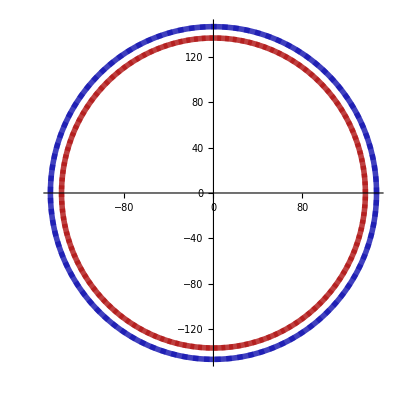
{-Graphics-,-Graphics-}

```mathematica
thk=0.01;style={Directive[Darker[Red],Thickness[thk],Dashing[0.007],Opacity[0.5]],Directive[Darker[Blue],Thickness[thk],Dashing[0.01],Opacity[0.5]],(**)Directive[Darker[Red],Thickness[thk],Opacity[0.75]],Directive[Darker[Blue],Thickness[thk],Opacity[0.75]]};
mu=10.0^-0; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ;   bohrrm= 3*10^-7 ;bval=100;
rot=-π/2;
sval=1 ;

p1=PolarPlot[{(√(v0val^2+4 cval mu)-v0val)/(2 cval),(√(v0val^2+4 cval mu)+v0val)/(2 cval),kF[bval,mu,cval,v0val,1,bohrrm,θ+rot,omval],kF[bval,mu,cval,v0val,-1,bohrrm,θ+rot,omval]},{θ,0,2π},PlotStyle->style];
sval=-1 ;
p2=PolarPlot[{(√(v0val^2+4 cval mu)-v0val)/(2 cval),(√(v0val^2+4 cval mu)+v0val)/(2 cval),kF[bval,mu,cval,v0val,1,bohrrm,θ+rot,omval],kF[bval,mu,cval,v0val,-1,bohrrm,θ+rot,omval]},{θ,0,2π},PlotStyle->style];
{p1,p2}
```

## phys quantities

```mathematica
Print["zeroth band vel, vvec:"]
vvec = FullSimplify[Grad[ c  (kx^2+ky^2+kz^2)+s v0 √(kx^2+ky^2+kz^2),{kx,ky,kz}],ass];
vvec=FullSimplify[FullSimplify[vvec/.repl,ass]/.srep]
```

zeroth band vel, vvec:

{Cos[ϕ] (s v0+2 c kf1[θ]) Sin[θ],(s v0+2 c kf1[θ]) Sin[θ] Sin[ϕ],Cos[θ] (s v0+2 c kf1[θ])}

```mathematica
Clear[s,mvec,Bvec,kf,dotprod];
mvec=(-e v0 { kx,ky,kz})/(2(kx^2+ky^2+kz^2)) (* -Graphics-*);
Bvec=B{0,0,1};
Print["BC vector:"](* -Graphics- *);
Ωvec=-s/(2(kf1[θ])^3)FullSimplify[{kx,ky,kz}/.repl,Assumptions->ass]/.srep
Print["omm energy:"];
 dotprod=-mvec.Bvec;
FullSimplify[dotprod/.repl,ass]/.srep
Print["omm velocity:"];
 vomm=om FullSimplify[Grad[dotprod,{kx,ky,kz}]/.kx^2->kf^2-kz^2-ky^2,ass]
vomm=FullSimplify[vomm/.repl]/.srep

Print["tot vel. velocity"];
vtot=(vomm+vvec)//FullSimplify

Print["vtot.k:"];
kf1[θ]FullSimplify[vtot.{ Cos[ϕ] Sin[θ],Sin[ϕ] Sin[θ],Cos[θ]}]
Print["Ω.vtot:"];
FullSimplify[Expand[vtot.Ωvec]/.s^2->1]
```

BC vector:

{-(s Cos[ϕ] Sin[θ])/(2 kf1[θ]^2),-(s Sin[θ] Sin[ϕ])/(2 kf1[θ]^2),-(s Cos[θ])/(2 kf1[θ]^2)}

omm energy:

(B e v0 Cos[θ])/(2 kf1[θ])

omm velocity:

{-(B e kx kz om v0)/kf^4,-(B e ky kz om v0)/kf^4,(B e (kf^2-2 kz^2) om v0)/(2 kf^4)}

{-(B e om v0 Cos[θ] Cos[ϕ] Sin[θ])/kf1[θ]^2,-(B e om v0 Cos[θ] Sin[θ] Sin[ϕ])/kf1[θ]^2,-(B e om v0 Cos[2 θ])/(2 kf1[θ]^2)}

tot vel. velocity

{vvec-(B e om v0 Cos[θ] Cos[ϕ] Sin[θ])/kf1[θ]^2,vvec-(B e om v0 Cos[θ] Sin[θ] Sin[ϕ])/kf1[θ]^2,vvec-(B e om v0 Cos[2 θ])/(2 kf1[θ]^2)}

vtot.k:

kf1[θ] (-(B e om v0 Cos[θ])/(2 kf1[θ]^2)+vvec (Cos[θ]+Sin[θ] (Cos[ϕ]+Sin[ϕ])))

Ω.vtot:

(s (B e om v0 Cos[θ]-2 vvec kf1[θ]^2 (Cos[θ]+Sin[θ] (Cos[ϕ]+Sin[ϕ]))))/(4 kf1[θ]^4)

```mathematica
Clear[x];
TeXForm[(e  B v0)/kf^4/.{kf->Subscript[k, F],v0->Subscript[v, 0]}]
{-kx kz,- ky kz,(kf^2-2 kz^2 )/2}/.{kf->Subscript[k, F], kx->Subscript[k, x], ky->Subscript[k, y],kz->Subscript[k, z]}
```

{-k_x k_z,-k_y k_z,1/2 (k_F^2-2 k_z^2)}

\frac{B e v_0}{k_F^4}

## sigma trials

```mathematica
Clear[sig,s,c,μ,B,v0];
sig[B_,μ_,c_,v0_,{βintra_,βinter_},mbohr_,om_]:=Block[{e=1,kf1vec,kf2vec,matr,bc1,bc2,θ,τ1,τ2,kf1,ϕ=0,kf2,f1,f2,vvec1,vvec2,vmm1,vmm2,vdotk1,vdotk2,conteq,λ1,λ2,a1,a2,cost,θp,s,Dphase1,Dphase2,h1,vz1,h2,vz2,zero1,zero2,ct1,ct2,ctct1,ctct2,hzero1,hzero2,hct1,hct2,hstcp1,hstcp2,hstsp1,hstsp2,colvec,mat,sol,sol1,Λ1,Λ2,s1,s2,int1,int2},
(* band 1 *)
s=1;
kf1[θ_]=(*ifun[B,μ,c,v0,s,mbohr,om][θ]*)kF[B,μ,c,v0,s,mbohr,θ,om];
(* kF[B_,μ_,c_,v0_,s_,mbohr_,θ_,om_] *)
bc1[θ_]=(-s om)/(2 ( kf1[θ])^2){ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
Dphase1[θ_]=1 +e {0,0,B}.bc1[θ] (*-Graphics-*);
vvec1[θ_]= (2 c kf1[θ]+s v0){ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm1[θ_]=(- om B e v0)/(2 kf1[θ]^2){Cos[ϕ] Sin[2θ],Sin[2θ] Sin[ϕ], Cos[2 θ]};
vdotk1[θ_]=(-B e om v0 Cos[θ])/(2 kf1[θ])+s v0 kf1[θ]+2 c kf1[θ]^2;
(* -Graphics-*)
h1[θ_]=1/Dphase1[θ]( (vvec1[θ]+vmm1[θ])[[3]]+ e B(bc1[θ].(vvec1[θ]+vmm1[θ])) );
(*****************)

(* band 2 *)
s=-1;
kf2[θ_]=kF[B,μ,c,v0,s,mbohr,θ,om];
bc2[θ_]=(-s om)/(2 ( kf2[θ])^2){ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
Dphase2[θ_]=1 +e {0,0,B}.bc2[θ] (*-Graphics-*);
vvec2[θ_]= (2 c kf2[θ]+s v0){ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm2[θ_]=(- om B e v0)/(2 kf2[θ]^2){Cos[ϕ] Sin[2θ],Sin[2θ] Sin[ϕ], Cos[2 θ]};
vdotk2[θ_]=(-B e om v0 Cos[θ])/(2 kf2[θ])+s v0 kf2[θ]+2 c kf2[θ]^2;
h2[θ_]=1/Dphase2[θ]( (vvec2[θ]+vmm2[θ])[[3]]+ e B(bc2[θ].(vvec2[θ]+vmm2[θ])));
(*****************)
(* -Graphics- *)
τ1[θ_]=(βintra/2 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp],{θp,0,π}]+
(βintra   Cos[θ])/2 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp],{θp,0,π}]+βinter/2 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp],{θp,0,π}]+(- βinter Cos[θ])/2 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[θp],{θp,0,π}])^-1;
(**************)
τ2[θ_]=(βintra/2 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp],{θp,0,π}]+
(βintra   Cos[θ])/2 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[θp],{θp,0,π}]+βinter/2 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp],{θp,0,π}]+(- βinter Cos[θ])/2 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp],{θp,0,π}])^-1;

(******************)
f1[θ_]=(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]] Dphase1[θ] τ1[θ];
f2[θ_]=(Sin[θ] (kf2[θ])^3)/Abs[vdotk2[θ]] Dphase2[θ] τ2[θ];
zero1=Quiet[NIntegrate [f1[θp],{θp,0,π}]];
zero2=Quiet[NIntegrate [f2[θp],{θp,0,π}]];
ct1=Quiet[NIntegrate [f1[θp] Cos[θp],{θp,0,π}]];
ct2=Quiet[NIntegrate [f2[θp] Cos[θp],{θp,0,π}]];
ctct1=Quiet[NIntegrate [f1[θp] Cos[θp]^2,{θp,0,π}]];
ctct2=Quiet[NIntegrate [f2[θp] Cos[θp]^2,{θp,0,π}]];

hzero1=Quiet[NIntegrate [f1[θp] h1[θp],{θp,0,π}]];
hzero2=Quiet[NIntegrate [f2[θp]h2[θp],{θp,0,π}]];
hct1=Quiet[NIntegrate [f1[θp]h1[θp]Cos[θp],{θp,0,π}]];
hct2=Quiet[NIntegrate [f2[θp]h2[θp]Cos[θp],{θp,0,π}]];

colvec=({{1/2 (hzero2 βinter+hzero1 βintra)}, {1/2 (-hct2 βinter+hct1 βintra)}, {1/2 (hzero1 βinter+hzero2 βintra)}, {1/2 (-hct1 βinter+hct2 βintra)}});
mat=({{1-(zero1 βintra)/2, -(ct1 βintra)/2, -(zero2 βinter)/2, -(ct2 βinter)/2}, {-(ct1 βintra)/2, 1-(ctct1 βintra)/2, (ct2 βinter)/2, (ctct2 βinter)/2}, {-(zero1 βinter)/2, -(ct1 βinter)/2, 1-(zero2 βintra)/2, -(ct2 βintra)/2}, {(ct1 βinter)/2, (ctct1 βinter)/2, -(ct2 βintra)/2, 1-(ctct2 βintra)/2}});

{mat,colvec,(*3*){{ zero1,-hzero1, ct1},{ zero2,-hzero2, ct2}},(*4*){f1[θ],h1[θ],f2[θ],h2[θ]},B,MatrixRank[mat]}
];
(* sig[B_,μ_,c_,v0_,{βintra_,βinter_},mbohr_,om_] *)
```

```mathematica
mu=10.0^-1; cval=5.0 10^-4 ;v0val= 5.0 10^-4; bohrrm= 3.0*10^-7 ;bval=10;vin=1;
Quiet[sig[bval,mu,cval,v0val,{vin,vin 0.5},bohrrm,1]]
```

```mathematica
Clear[sigt,s,c,μ,B,v0];
sigt[B_,μ_,c_,v0_,{βintra_,βinter_},mbohr_]:=Block[{θ,s1,s2,cs1,cs2,b1,b2,c1,c2,bt,ct,λ1,a1,λ2,a2,λb1,ab1,λb2,ab2,mat, sol,f1,f2,h1,h2,int1,int2,sz1,sz2},
(* sig[B_,μ_,c_,v0_,{βintra_,βinter_},mbohr_,om_] gives  {mat,colvec,{{ zero1,-hzero1, ct1},(**){ zero2,-hzero2, ct2}},B,MatrixRank[mat]} *)
s1=sig[B,μ,c,v0,{βintra,βinter},mbohr,1];
s2=sig[B,μ,c,v0,{βintra,βinter},mbohr,-1];
cs1=s1[[3,1]].{λ1,1,a1}+s2[[3,1]].{λb1,1,ab1};
cs2=s1[[3,2]].{λ2,1,a2}+s2[[3,2]].{λb2,1,ab2};
c1=s1[[2]];b1=s1[[1]];
c2=s2[[2]];b2=s2[[1]];
bt=ArrayFlatten[{{b1,0},{0,b2}}];(*Print[bt//MatrixForm];*)
ct=Join[c1,c2];(*Print[ct//MatrixForm];*)
mat=bt.{λ1,a1,λ2,a2,λb1,ab1,λb2,ab2};
sol=Flatten[Solve[{mat[[1]]+ct[[1]]==0,mat[[2]]+ct[[2]]==0,mat[[3]]+ct[[3]]==0,mat[[4]]+ct[[4]]==0,mat[[5]]+ct[[5]]==0,mat[[7]]+ct[[7]]==0,mat[[8]]+ct[[8]]==0,cs1==0,cs2==0},{λ1,a1,λ2,a2,λb1,ab1,λb2,ab2}],1];

f1[θ_]=s1[[4,1]];f2[θ_]=s1[[4,3]];
h1[θ_]=s1[[4,2]];h2[θ_]=s1[[4,4]];
int1[θ_]=-f1[θ]h1[θ](λ1-h1[θ]+a1 Cos[θ])/.sol;
int2[θ_]=-f2[θ]h2[θ](λ2-h2[θ]+a2 Cos[θ])/.sol;
sz1={NIntegrate[int1[θ],{θ,0,π}], NIntegrate[int2[θ],{θ,0,π}]};
f1[θ_]=s2[[4,1]];f2[θ_]=s2[[4,3]];
h1[θ_]=s2[[4,2]];h2[θ_]=s2[[4,4]];
int1[θ_]=-f1[θ]h1[θ](λb1-h1[θ]+ab1 Cos[θ])/.sol;
int2[θ_]=-f2[θ]h2[θ](λb2-h2[θ]+ab2 Cos[θ])/.sol;
sz2={NIntegrate[int1[θ],{θ,0,π}], NIntegrate[int2[θ],{θ,0,π}]};

{B,sz1,sz2,sol}
];
mu=10.0^-1; cval=5.0 10^-4 ;v0val= 5.0 10^-4; bohrrm= 3.0*10^-7 ;bval=20;vin=1;
Quiet[sigt[bval,mu,cval,v0val,{vin,vin 0.5},bohrrm]]//Chop
```

{20,{0.0000911815,0},{0.000094074,0},{λ1→0.000802909,a1→-0.00140216,λ2→0.00017915,a2→-0.00213579,λb1→-0.000802909,ab1→-0.00140216,λb2→-0.00017915,ab2→-0.00213579}}

## sigma final

```mathematica
Clear[sign,s,c,μ,B,v0];
sign[B_,μ_,c_,v0_,{βintra_,βinter_},mbohr_,om_]:=Block[{e=1,kf1vec,kf2vec,matr,bc1,bc2,θ,τ1,τ2,kf1,ϕ=0,kf2,f1,f2,vvec1,vvec2,vmm1,vmm2,vdotk1,vdotk2,conteq,λ1,λ2,a1,a2,cost,θp,s,Dphase1,Dphase2,h1,vz1,h2,vz2,zero1,zero2,ct1,ct2,ctct1,cs,ctct2,hzero1,hzero2,hct1,hct2,hstcp1,hstcp2,hstsp1,hstsp2,colvec,mat,sol,sol1,Λ1,Λ2,s1,s2,int1,int2},
(* band 1 *)
s=1;
kf1[θ_]=(*ifun[B,μ,c,v0,s,mbohr,om][θ]*)kF[B,μ,c,v0,s,mbohr,θ,om];
(* kF[B_,μ_,c_,v0_,s_,mbohr_,θ_,om_] *)
bc1[θ_]=(-s om)/(2 ( kf1[θ])^2){ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
Dphase1[θ_]=1 +e {0,0,B}.bc1[θ] (*-Graphics-*);
vvec1[θ_]= (2 c kf1[θ]+s v0){ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm1[θ_]=(- om B e v0)/(2 kf1[θ]^2){Cos[ϕ] Sin[2θ],Sin[2θ] Sin[ϕ], Cos[2 θ]};
vdotk1[θ_]=(-B e om v0 Cos[θ])/(2 kf1[θ])+s v0 kf1[θ]+2 c kf1[θ]^2(* kf1[θ] (s v0-(B e om v0 Cos[θ])/(2 kf1[θ]^2)+2 c kf1[θ]) *);
(* -Graphics-*)
h1[θ_]=1/Dphase1[θ]( (vvec1[θ]+vmm1[θ])[[3]]+ e B(bc1[θ].(vvec1[θ]+vmm1[θ])) );
(*****************)

(* band 2 *)
s=-1;
kf2[θ_]=kF[B,μ,c,v0,s,mbohr,θ,om];
bc2[θ_]=(-s om)/(2 ( kf2[θ])^2){ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
Dphase2[θ_]=1 +e {0,0,B}.bc2[θ] (*-Graphics-*);
vvec2[θ_]= (2 c kf2[θ]+s v0){ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm2[θ_]=(- om B e v0)/(2 kf2[θ]^2){Cos[ϕ] Sin[2θ],Sin[2θ] Sin[ϕ], Cos[2 θ]};
vdotk2[θ_]=(-B e om v0 Cos[θ])/(2 kf2[θ])+s v0 kf2[θ]+2 c kf2[θ]^2;
h2[θ_]=1/Dphase2[θ]( (vvec2[θ]+vmm2[θ])[[3]]+ e B(bc2[θ].(vvec2[θ]+vmm2[θ])));
(*****************)
(* -Graphics- *)
τ1[θ_]=(βintra/2 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp],{θp,0,π}]+
(βintra   Cos[θ])/2 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp],{θp,0,π}]+βinter/2 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp],{θp,0,π}]+(- βinter Cos[θ])/2 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[θp],{θp,0,π}])^-1;
(**************)
τ2[θ_]=(βintra/2 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp],{θp,0,π}]+
(βintra   Cos[θ])/2 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[θp],{θp,0,π}]+βinter/2 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp],{θp,0,π}]+(- βinter Cos[θ])/2 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp],{θp,0,π}])^-1;

(******************)
f1[θ_]=(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]] Dphase1[θ] τ1[θ];
f2[θ_]=(Sin[θ] (kf2[θ])^3)/Abs[vdotk2[θ]] Dphase2[θ] τ2[θ];
zero1=Quiet[NIntegrate [f1[θp],{θp,0,π}]];
zero2=Quiet[NIntegrate [f2[θp],{θp,0,π}]];
ct1=Quiet[NIntegrate [f1[θp] Cos[θp],{θp,0,π}]];
ct2=Quiet[NIntegrate [f2[θp] Cos[θp],{θp,0,π}]];
ctct1=Quiet[NIntegrate [f1[θp] Cos[θp]^2,{θp,0,π}]];
ctct2=Quiet[NIntegrate [f2[θp] Cos[θp]^2,{θp,0,π}]];

hzero1=Quiet[NIntegrate [f1[θp] h1[θp],{θp,0,π}]];
hzero2=Quiet[NIntegrate [f2[θp]h2[θp],{θp,0,π}]];
hct1=Quiet[NIntegrate [f1[θp]h1[θp]Cos[θp],{θp,0,π}]];
hct2=Quiet[NIntegrate [f2[θp]h2[θp]Cos[θp],{θp,0,π}]];

colvec=({{1/2 (hzero2 βinter+hzero1 βintra)}, {1/2 (-hct2 βinter+hct1 βintra)}, {1/2 (hzero1 βinter+hzero2 βintra)}, {1/2 (-hct1 βinter+hct2 βintra)}});
mat=({{1-(zero1 βintra)/2, -(ct1 βintra)/2, -(zero2 βinter)/2, -(ct2 βinter)/2}, {-(ct1 βintra)/2, 1-(ctct1 βintra)/2, (ct2 βinter)/2, (ctct2 βinter)/2}, {-(zero1 βinter)/2, -(ct1 βinter)/2, 1-(zero2 βintra)/2, -(ct2 βintra)/2}, {(ct1 βinter)/2, (ctct1 βinter)/2, -(ct2 βintra)/2, 1-(ctct2 βintra)/2}});
matr=mat.{λ1,a1,λ2,a2};
cs=λ1 zero1-hzero1+a1 ct1+λ2 zero2-hzero2+a2 ct2;
sol=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[3]]+colvec[[3]]==0,matr[[4]]+colvec[[4]]==0,cs==0},{λ1,a1,λ2,a2}],1];
Λ1[θ_]=(λ1-h1[θ]+a1 Cos[θ])/.sol;
int1[θ_]=-f1[θ]h1[θ]Λ1[θ];
s1=NIntegrate[int1[θ],{θ,0,π}];

Λ2[θ_]=(λ2-h2[θ]+a2 Cos[θ])/.sol;
int2[θ_]=-f2[θ]h2[θ]Λ2[θ];
s2=NIntegrate[int2[θ],{θ,0,π}];
{B,s1,s2}
];
(* sig[B_,μ_,c_,v0_,{βintra_,βinter_},mbohr_,om_] *)
```

```mathematica
mu=10.0^0; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;in=1;
sign[1,mu,cval,v0val,{in,0.0001in}, bohrrm,omval]
```

{1,0.000200207,0.000200215}

```mathematica
mu=10.0^0; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;in=1;
dat=Table[sign[B,mu,cval,v0val,{in,10^-7 in}, bohrrm,omval],{B,-25,25,10}]
```

{{-25,0.00103768,0.000927269},{-15,0.000501727,0.000461976},{-5,0.000233748,0.00022933},{5,0.000233747,0.000229331},{15,0.000501726,0.000461977},{25,0.00103769,0.000927267}}

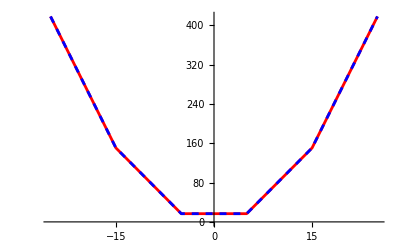

```mathematica
(* mu=10.0^0; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;in=1;
sign[1,mu,cval,v0val,{in, 10^-7 in}, bohrrm,omval], matr[[1]] considered *)list={{-25,0.001037682754025493,0.0009272690723837185},{-15,0.0005017266135576848,0.00046197612574869207},{-5,0.0002337476151665005,0.0002293304084568376},{5,0.00023374706933644573,0.00022933096783986362},{15,0.0005017262675031109,0.00046197682955900765},{25,0.0010376864862174928,0.0009272669983191872}};
len=Length[list];
x=1/0.00020023858774208107;
dt1=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^2},{i,1,len}];
x=1/0.00020024329228958833;
dt2=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^2},{i,1,len}];
ListLinePlot[{dt1,dt2},PlotStyle->{Directive[Red],Directive[Blue,Dashed]}]
```

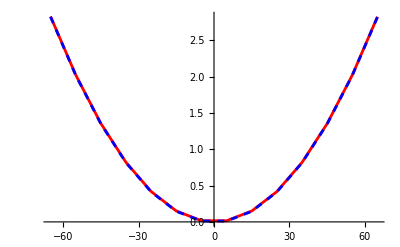

```mathematica
(* mu=10.0^0; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;in=1;
sign[1,mu,cval,v0val,{in,0.0001in}, bohrrm,omval], matr[[1]] considered *)list={{-65,0.00020586907751248766,0.00020512371952149402},{-55,0.00020426097281161333,0.00020372870725664542},{-45,0.00020292078218408084,0.0002025662992531864},{-35,0.00020184850700587215,0.00020163649465220948},{-25,0.0002010441486389076,0.00020093929257180985},{-15,0.00020050770842247397,0.00020047469210705514},{-5,0.00020023918768735392,0.00020024269232997715},{5,0.0002002385877421159,0.00020024329228958827},{15,0.00020050590987592611,0.000200476491011851},{25,0.00020104115536638342,0.0002009422874997226},{35,0.00020184432547245548,0.0002016406807330995},{45,0.00020291542143328353,0.00020257166966890938},{55,0.00020425444447634013,0.00020373525324099374},{65,0.0002058613958045444,0.00020513143036018943}};
len=Length[list];
x=1/0.00020020667714191776;
dt1=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^2},{i,1,len}];
x=1/0.0002002151403991716;
dt2=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^2},{i,1,len}];
ListLinePlot[{dt1,dt2},PlotStyle->{Directive[Red],Directive[Blue,Dashed]}]
```

## sigma at B=0

```mathematica
Solve[k ( c k+s v0)==μ,k]/.s^2->1
```

{{k→(-s v0-√(v0^2+4 c μ))/(2 c)},{k→(-s v0+√(v0^2+4 c μ))/(2 c)}}

```mathematica
Clear[sig0,s,c,μ,B,v0];
sig0[μ_,c_,v0_,{βintra_,βinter_}]:=Block[{e=1,B=0,kf1vec,kf2vec,matr,bc1,bc2,θ,τ1,τ2,kf1,ϕ=0,kf2,f1,f2,vvec1,vvec2,vmm1,vmm2,vdotk1,vdotk2,conteq,λ1,λ2,a1,a2,cost,θp,s,Dphase1,Dphase2,h1,vz1,h2,vz2,zero1,zero2,ct1,ct2,ctct1,cs,ctct2,hzero1,hzero2,hct1,hct2,hstcp1,hstcp2,hstsp1,hstsp2,colvec,mat,sol,sol1,Λ1,Λ2,s1,s2,int1,int2},
(* band 1 *)
s=1;
kf1[θ_]=(-s v0+√(v0^2+4 c μ))/(2 c);
Dphase1[θ_]=1  ;
vvec1[θ_]= (2 c kf1[θ]+s v0){ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm1[θ_]={0,0,0};
vdotk1[θ_]=s v0 kf1[θ]+2 c kf1[θ]^2;
h1[θ_]=1/Dphase1[θ](vvec1[θ])[[3]] ;
(*****************)

(* band 2 *)
s=-1;
kf2[θ_]=(-s v0+√(v0^2+4 c μ))/(2 c);
bc2[θ_]={ 0,0,0};
Dphase2[θ_]=1 ;
vvec2[θ_]= (2 c kf2[θ]+s v0){ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm2[θ_]={0,0,0};
vdotk2[θ_]=s v0 kf2[θ]+2 c kf2[θ]^2;
h2[θ_]=1/Dphase2[θ](vvec2[θ])[[3]];
(*****************)
τ1[θ_]=(βintra/2 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp],{θp,0,π}]+
(βintra   Cos[θ])/2 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp],{θp,0,π}]+βinter/2 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp],{θp,0,π}]+(- βinter Cos[θ])/2 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[θp],{θp,0,π}])^-1;
(**************)
τ2[θ_]=(βintra/2 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp],{θp,0,π}]+
(βintra   Cos[θ])/2 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[θp],{θp,0,π}]+βinter/2 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp],{θp,0,π}]+(- βinter Cos[θ])/2 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp],{θp,0,π}])^-1;

(******************)
f1[θ_]=(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]] Dphase1[θ] τ1[θ];
f2[θ_]=(Sin[θ] (kf2[θ])^3)/Abs[vdotk2[θ]] Dphase2[θ] τ2[θ];
zero1=Quiet[NIntegrate [f1[θp],{θp,0,π}]];
zero2=Quiet[NIntegrate [f2[θp],{θp,0,π}]];
ct1=Quiet[NIntegrate [f1[θp] Cos[θp],{θp,0,π}]];
ct2=Quiet[NIntegrate [f2[θp] Cos[θp],{θp,0,π}]];
ctct1=Quiet[NIntegrate [f1[θp] Cos[θp]^2,{θp,0,π}]];
ctct2=Quiet[NIntegrate [f2[θp] Cos[θp]^2,{θp,0,π}]];

hzero1=Quiet[NIntegrate [f1[θp] h1[θp],{θp,0,π}]];
hzero2=Quiet[NIntegrate [f2[θp]h2[θp],{θp,0,π}]];
hct1=Quiet[NIntegrate [f1[θp]h1[θp]Cos[θp],{θp,0,π}]];
hct2=Quiet[NIntegrate [f2[θp]h2[θp]Cos[θp],{θp,0,π}]];

colvec=({{1/2 (hzero2 βinter+hzero1 βintra)}, {1/2 (-hct2 βinter+hct1 βintra)}, {1/2 (hzero1 βinter+hzero2 βintra)}, {1/2 (-hct1 βinter+hct2 βintra)}});
mat=({{1-(zero1 βintra)/2, -(ct1 βintra)/2, -(zero2 βinter)/2, -(ct2 βinter)/2}, {-(ct1 βintra)/2, 1-(ctct1 βintra)/2, (ct2 βinter)/2, (ctct2 βinter)/2}, {-(zero1 βinter)/2, -(ct1 βinter)/2, 1-(zero2 βintra)/2, -(ct2 βintra)/2}, {(ct1 βinter)/2, (ctct1 βinter)/2, -(ct2 βintra)/2, 1-(ctct2 βintra)/2}});
matr=mat.{λ1,a1,λ2,a2};
cs=λ1 zero1-hzero1+a1 ct1+λ2 zero2-hzero2+a2 ct2;
sol=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,matr[[3]]+colvec[[3]]==0,matr[[4]]+colvec[[4]]==0,cs==0},{λ1,a1,λ2,a2}],1];
Λ1[θ_]=(λ1-h1[θ]+a1 Cos[θ])/.sol;
int1[θ_]=-f1[θ]h1[θ]Λ1[θ];
s1=NIntegrate[int1[θ],{θ,0,π}];

Λ2[θ_]=(λ2-h2[θ]+a2 Cos[θ])/.sol;
int2[θ_]=-f2[θ]h2[θ]Λ2[θ];
s2=NIntegrate[int2[θ],{θ,0,π}];
{0,s1,s2}
];
(* sig[B_,μ_,c_,v0_,{βintra_,βinter_},mbohr_,om_] *)
mu=10.0^0; cval=5 10^-5 ;v0val= 5 10^-4; in=1;
Quiet[sig0[mu,cval,v0val,{in,0.5 in}]]
```

{0,0.0000930583,0.000107192}

## Results

### set 1

```mathematica
mu=10.0^0; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;in=1;
dat=Table[sign[B,mu,cval,v0val,{in,0.5 in}, bohrrm,omval],{B,-105,-5,10}]
```

{{-105,0.0000930649,0.000107188},{-95,0.0000930641,0.000107188},{-85,0.0000930634,0.000107188},{-75,0.0000930627,0.000107188},{-65,0.000093062,0.000107189},{-55,0.0000930614,0.000107189},{-45,0.0000930608,0.00010719},{-35,0.0000930602,0.00010719},{-25,0.0000930596,0.00010719},{-15,0.0000930591,0.000107191},{-5,0.0000930586,0.000107191}}

```mathematica
sign[0.01,mu,cval,v0val,{in,0.5 in}, bohrrm,omval]
```

{0.01,0.0000930583,0.000107192}

```mathematica
Quiet[sig0[mu,cval,v0val,{in,0.5 in}]]
```

{0,0.0000930583,0.000107192}

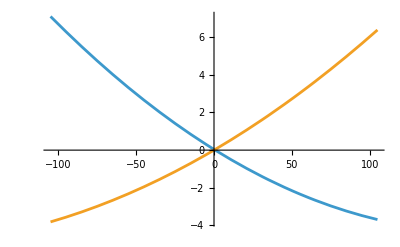

```mathematica
list=Sort[{{-105,0.00009306490936629008,0.00010718757591236421},{-95,0.00009306414966343676,0.00010718784645718133},{-85,0.00009306341810985735,0.0001071881420032009},{-75,0.00009306271470571438,0.00010718846255028283},{-65,0.00009306203945116048,0.00010718880809827079},{-55,0.00009306139234628808,0.00010718917864701979},{-45,0.00009306077339132098,0.00010718957419638825},{-35,0.00009306018258634946,0.00010718999474623722},{-25,0.00009305961993151154,0.00010719044029642864},{-15,0.00009305908542705033,0.0001071909108468141},{-5,0.00009305857907302804,0.00010719140639727258},{0,0.00009305833645251493,0.00010719166354748506},{0.01,0.00009305833943573671,0.00010719166405825704},{1,0.00009305828877166297,0.00010719171572772005},{11,0.00009305782745989764,0.00010719225127783677},{21,0.00009305739429811975,0.00010719281182782214},{31,0.00009305698928732778,0.00010719339737742098},{35,0.00009305683516529465,0.00010719363859712963},{45,0.00009305646956634436,0.00010719425914595889},{55,0.0000930561321188686,0.00010719490469409494},{65,0.00009305582282316988,0.00010719557524140218},{75,0.00009305554167934364,0.00010719627078777916},{85,0.00009305528868765387,0.00010719699133309863},{95,0.00009305506384828286,0.00010719773687725394},{105,0.00009305486716141603,0.00010719850742013109},{51,0.00009305626371965635,0.0001071946434749328},{61,0.00009305594316320567,0.00010719530402258816}}];
len=Length[list];
x=1/0.0000930583;
d1at11=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^5},{i,1,len}];
x=1/0.00010719166354748506;
d1at12=Table[{list[[i,1]],(Re[list[[i,3]]]x-1)10^5},{i,1,len}];
ListLinePlot[{d1at11,d1at12}]
```

```mathematica
mu=10.0^0; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;in=1;
dat=Table[sign[B,mu,cval,v0val,{in, in}, bohrrm,omval],{B,-105,-5,10}]
```

{{-105,0.0000598541,0.0000739789},{-95,0.0000598536,0.0000739793},{-85,0.0000598531,0.0000739796},{-75,0.0000598527,0.00007398},{-65,0.0000598522+1.00203×10^-11 ⅈ,0.0000739803},{-55,0.0000598518,0.0000739807},{-45,0.0000598514,0.0000739811},{-35,0.000059851,0.0000739815},{-25,0.0000598506,0.0000739819},{-15,0.0000598502,0.0000739823},{-5,0.0000598498,0.0000739827}}

```mathematica
sign[0.01,mu,cval,v0val,{in, in}, bohrrm,omval]
```

{0.01,0.0000598496,0.0000739829}

```mathematica
Quiet[sig0[mu,cval,v0val,{in,in}]]
```

{0,0.0000598496,0.0000739829}

```mathematica
list={{-105,0.000059854079577433605,0.00007397893583798363},{-95,0.000059853600999723307,0.00007397927033390534},{-85,0.000059853133113322764,0.00007397961418945067},{-75,0.000059852675918269816,0.00007397996740455504},{-65,0.000059852232347131954,0.00007398032997912442},{-55,0.00005985179360258636,0.00007398070191308776},{-45,0.000059851368482125414,0.00007398108320636254},{-35,0.00005985095405330319,0.00007398147385888659},{-25,0.00005985055031628488,0.00007398187387056801},{-15,0.000059850157271128024,0.00007398228324134157},{-5,0.00005984977491796357,0.00007398270197112708},{0,0.00005984958775070338,0.00007398291484567346},{0.01,0.000059849587380925666,0.00007398291527335935},{1,0.000059849550637895864,0.00007398295770137836},{11,0.00005984918539208254,0.00007398339140544629},{21,0.00005984883083829231,0.00007398383404929785},{31,0.00005984848697672649,0.00007398428689014118},{41,0.00005984815380755479,0.00007398474866992505},{51,0.000059847831330864755,0.00007398521980971958},{61,0.00005984751954672159,0.00007398570030744047},{75,0.00005984710101265042,0.00007398638872658465},{85,0.000059846814891106236,0.00007398689168470983},{95,0.000059846539462518015,0.00007398740400124098},{105,0.00005984627472696276,0.0000739879256761289}};
len=Length[list];
x=1/0.00005984958775070338;
d1at21=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^5},{i,1,len}];
x=1/0.00007398291484567346;
d1at22=Table[{list[[i,1]],(Re[list[[i,3]]]x-1)10^5},{i,1,len}];
ListLinePlot[{d1at21,d1at22}];
```

```mathematica
mu=10.0^0; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;in=1;
dat=Table[sign[B,mu,cval,v0val,{in,2 in}, bohrrm,omval],{B,-105,-5,10}]
```

```mathematica
sign[100,mu,cval,v0val,{in,2 in}, bohrrm,omval]
```

{100,0.0000346283,0.0000459519}

```mathematica
Quiet[sig0[mu,cval,v0val,{in,2in}]]
```

{0,0.0000346307,0.0000459486}

```mathematica
list={{-105,0.00003463356428652379,0.00004594557279837709},{-95,0.000034633268962325616,0.00004594584520798432},{-85,0.000034632977819963356,0.000045946121149965626},{-75,0.00003463269085949277,0.00004594640062427846},{-65,0.00003463240808095598,0.000045946683630876684},{-55,0.00003463212948439139,0.00004594697016971761},{-45,0.00003463185506988033,0.00004594726024075413},{-35,0.00003463158483738829,0.00004594755384396593},{-25,0.000034631318787067356,0.00004594785097928399},{-15,0.000034631056918888976,0.000045948151646690866},{-5,0.00003463079923298347,0.000045948455846126066},{0,0.000034630671958311244,0.00004594860927036787},{0.01,0.00003463063824343998,0.00004594860958592459},{1,0.00003463064662843038,0.000045948640061292414},{11,0.00003463039563456884,0.00004594894991181268},{21,0.00003463014882265353,0.000045949263294395},{31,0.000034629906193133536,0.00004594958020889406},{51,0.0000346294334815695,0.000045950224633489976},{61,0.00003462920339966365,0.000045950552143513086},{75,0.00003462888831186278,0.00004595101659092579},{85,0.000034628668268405905,0.00004595135257716856},{95,0.00003462845240776462,0.00004595169209511359},{100,0.0000346283460460126,0.00004595186317846526}};
len=Length[list];
x=1/0.000034630671958311244;
d1at31=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^5},{i,1,len}];
x=1/0.00004594860958592459;
d1at32=Table[{list[[i,1]],(Re[list[[i,3]]]x-1)10^5},{i,1,len}];
ListLinePlot[{d1at31,d1at32}];
```

```mathematica
mu=10.0^0; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;in=1;
dat=Table[sign[B,mu,cval,v0val,{in,50in}, bohrrm,omval],{B,-105,-5,10}]
```

```mathematica
sign[0.01,mu,cval,v0val,{in,50in}, bohrrm,omval]
```

```mathematica
Quiet[sig0[mu,cval,v0val,{in,50in}]]
```

{0,1.59777×10^-6,2.42479×10^-6}

```mathematica
list={{-105,1.5979371984059414*^-6,2.42458277998223*^-6},{-95,1.5979207282144715*^-6,2.4246021549014493*^-6},{-85,1.5979043730908837*^-6,2.4246216154986345*^-6},{-75,1.5978881330374412*^-6,2.4246411617721855*^-6},{-65,1.5978720080575494*^-6,2.4246607937196784*^-6},{-55,1.5978559981520757*^-6,2.4246805113398372*^-6},{-45,1.59784010332728*^-6,2.4247003146295877*^-6},{-35,1.5978243235808717*^-6,2.4247202035889106*^-6},{-25,1.597808658919032*^-6,2.4247401782146933*^-6},{-15,1.5977931093445947*^-6,2.424760238505119*^-6},{-5,1.5977776748560427*^-6,2.42478038446009*^-6},{0,1.5977700007754203*^-6,2.424790489559188*^-6},(*{0.01,1.597767033550241*^-6,2.424790509420539*^-6},*){5,1.5977623554643933*^-6,2.4248006160748732*^-6},{15,1.5977471511681928*^-6,2.4248209333493796*^-6},{25,1.5977320619682628*^-6,2.4248413362827414*^-6},{35,1.5977170878668622*^-6,2.4248618248735106*^-6},{45,1.5977022288737314*^-6,2.424882399117777*^-6},{55,1.597687484986061*^-6,2.4249030590160174*^-6},{65,1.5976728562095311*^-6,2.4249238045657738*^-6},{75,1.5976583425465133*^-6,2.4249446357658695*^-6},{85,1.5976439440006305*^-6,2.4249655526146262*^-6},{95,1.597629660575675*^-6,2.424986555110499*^-6},{105,1.5976154922743104*^-6,2.4250076432521638*^-6}};
len=Length[list];
x=1/1.5977700007754203*^-6;
d1at41=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^5},{i,1,len}];
x=1/2.424790489559188*^-6;
d1at42=Table[{list[[i,1]],(Re[list[[i,3]]]x-1)10^5},{i,1,len}];
ListLinePlot[{d1at41,d1at42}];
```

```mathematica
mu=10.0^0; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;in=1;
dat=Table[sign[B,mu,cval,v0val,{in,200in}, bohrrm,omval],{B,5,65,10}]
```

```mathematica
list={{5,4.0107114969702904*^-7,6.125324551393724*^-7},{15,4.010672872469696*^-7,6.125376324336939*^-7},{25,4.010634531620745*^-7,6.12542830682178*^-7},{35,4.010596474418015*^-7,6.125480498848898*^-7},{45,4.0105587008847976*^-7,6.125532900408872*^-7},{55,4.010521211021387*^-7,6.125585511500173*^-7},{65,4.010484004834565*^-7,6.125638332119485*^-7}};
len=Length[list];
dat1=Table[{list[[i,1]],Re[list[[i,2]]]},{i,1,len}];
dat2=Table[{list[[i,1]],Re[list[[i,3]]]},{i,1,len}];
ListLinePlot[dat1]
ListLinePlot[dat2]
```

### set 2

```mathematica
mu=10.0^-1; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;in=1;rat1=0.5;
rat=rat1;
dat=Table[Quiet[sign[B,mu,cval,v0val,{in,rat in}, bohrrm,omval]]//Chop,{B,-100,-50,10}]
Quiet[sig0[mu,cval,v0val,{in,rat in}]]
```

{{-100,7.92247×10^-6,0.0000123528},{-90,0,0.0000123513},{-80,7.91594×10^-6,0.00001235},{-70,7.91315×10^-6,0.000012349},{-60,7.91068×10^-6,0.0000123481},{-50,7.90852×10^-6,0.0000123475}}

{0,7.90244×10^-6,0.0000123476}

```mathematica
mu=10.0^-1; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;in=1;rat1=0.5;
rat=rat1;sign[-85,mu,cval,v0val,{in,0.5 in}, bohrrm,omval]
```

{-85,7.91746×10^-6,0.0000123506}

```mathematica
list={{-100,7.922468068411161*^-6,0.000012352800398629593},{-95,7.920718521869717*^-6,0.000012352023554867786},{-85,7.917455709791421*^-6,0.000012350632491746564},{-80,7.915942436589134*^-6,0.000012350018267987904},{-70,7.913152139396545*^-6,0.000012348952425647526},{-60,7.910676823403933*^-6,0.000012348103376993344},{-50,7.908516472345012*^-6,0.000012347471106981993},{-60,7.910676823403933*^-6,0.000012348103376993344},{-50,7.908516472345012*^-6,0.000012347471106981993},{-40,7.90667107570763*^-6,0.000012347055601507928},{-30,7.905140628729032*^-6,0.00001234685684740066},{-20,7.90392513239823*^-6,0.000012346874832425314},{-10,7.903024593456038*^-6,0.000012347109545282712},{0.01,7.902438596141654*^-6,0.000012347561535559583},{1,7.902397791491892*^-6,0.000012347618037730523},{11,7.90215871057299*^-6,0.000012348307846423672},{21,7.902232915400417*^-6,0.000012349214353868478},{31,7.902625623604156*^-6,0.0000123503375526038},{41,7.903331683974776*^-6,0.000012351677484289842},{51,7.904352867478995*^-6,0.000012353233998780053},{61,7.905689221758412*^-6,0.00001235500723597068},{72,7.907523297639336*^-6,0.000012357208056897298},{82,7.909521691335568*^-6,0.000012359436294273},{92,7.911835440260618*^-6,0.00001236188120303727},{102,7.914464615805477*^-6,0.000012364542777041329}};
len=Length[list];
x=1/7.902439024390243*^-6;
d2at11=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^3},{i,1,len}];
x=1/0.000012347560975609756;
d2at12=Table[{list[[i,1]],(Re[list[[i,3]]]x-1)10^3},{i,1,len}];
ListLinePlot[{d2at11,d2at12},PlotRange->{{-100,100},{-0.1,1.5}}];
```

```mathematica
mu=10.0^-1; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;in=1;rat2=1;
rat=rat2;
Quiet[sig0[mu,cval,v0val,{in,rat in}]]//Chop
```

{0,4.69007×10^-6,9.13519×10^-6}

```mathematica
Quiet[sign[-85,mu,cval,v0val,{in,rat in}, bohrrm,omval]]//Chop
```

{-85,4.69716×10^-6,9.13401×10^-6}

```mathematica
list={{-105,4.7001256474149365*^-6,9.134588809556516*^-6},{-95,4.698582407182924*^-6,9.134257539976278*^-6},{-85,4.6971623852550255*^-6,9.134008040067606*^-6},{-70,4.695263347671542*^-6,9.13378708691537*^-6},{-60,4.6941512989222105*^-6,9.133741966773432*^-6},{-50,4.6931624191125135*^-6,9.133778580749028*^-6},{-40,4.692296701593458*^-6,9.133896920080797*^-6},{-30,4.691554143023224*^-6,9.134096976942394*^-6},{-20,4.690934743370967*^-6,9.134378744441792*^-6},{-10,4.690438505915369*^-6,9.134742216621511*^-6},{0,4.690065437239738*^-6,9.135187388459248*^-6},{0.01,4.690065126134614*^-6,9.135187874440284*^-6},{1,4.690034905008071*^-6,9.135236398958826*^-6},{11,4.689797333549066*^-6,9.135771435734116*^-6},{21,4.689682955480687*^-6,9.136388169707054*^-6},{31,4.689691787650912*^-6,9.137086583608746*^-6},{41,4.689823850227376*^-6,9.137866727118747*^-6},{51,4.690079166694438*^-6,9.138728487737959*^-6},{65,4.690643727957475*^-6,9.140072240888116*^-6},{72,4.6910166460052864*^-6,9.140804164495633*^-6},{82,4.691654234683001*^-6,9.141919199870619*^-6},{92,4.692415208307351*^-6,9.143115936500084*^-6},{102,4.693299607347001*^-6,9.14439437490433*^-6}};
len=Length[list];
x=1/4.690065437239738*^-6;
d2at21=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^3},{i,1,len}];
x=1/9.135187388459248*^-6;
d2at22=Table[{list[[i,1]],(Re[list[[i,3]]]x-1)10^3},{i,1,len}];
ListLinePlot[{d2at21,d2at22},PlotRange->{{-100,100},{-0.5,1.5}}];
```

```mathematica
mu=10.0^-1; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;in=1;rat3=2;rat=rat3;
dat=Table[Quiet[sign[B,mu,cval,v0val,{in,2 in}, bohrrm,omval]],{B,-105,-5,10}]
```

```mathematica
rat3=2;rat=rat3;
Quiet[sig0[mu,cval,v0val,{in,rat in}]]
```

{0,2.49111×10^-6,6.08181×10^-6}

```mathematica
list=Sort[{{-105,2.4960379710928383*^-6,6.0796590589854855*^-6},{-95,2.495326134857276*^-6,6.079714184055781*^-6},{-85,2.4946653699988302*^-6,6.079800877733139*^-6},{-75,2.49405566731302*^-6,6.079919133802611*^-6},{-65,2.493497019365333*^-6,6.080068946618418*^-6},{-55,2.4929894204886747*^-6,6.080250311103544*^-6},{-45,2.492532866782686*^-6,6.080463222751009*^-6},{-35,2.4921273561124885*^-6,6.0807227661861345*^-6+1.858634572844865*^-11 ⅈ},{-25,2.4917728881071077*^-6,6.080983672345997*^-6},{-15,2.4914694641618536*^-6,6.081291204121199*^-6},{-5,2.491217087435546*^-6,6.081630270714189*^-6},{0,2.491110043248439*^-6,6.081811629024508*^-6},{0.01,2.4911098421035545*^-6,6.081811999587289*^-6},{1,2.491090166037641*^-6,6.081848846666379*^-6},{11,2.490919475837642*^-6,6.082238365738688*^-6},{21,2.4907998712238263*^-6,6.082659416479941*^-6},{31,2.4907312960267723*^-6,6.083111998700027*^-6},{41,2.490713827215294*^-6,6.0835961365329405*^-6},{51,2.490747455945971*^-6,6.084111759660109*^-6},{61,2.490832197042874*^-6,6.084658940869513*^-6},{71,2.490968067102363*^-6,6.085237658460939*^-6},{81,2.491155084496456*^-6,6.085847915110815*^-6},{91,2.491393269376972*^-6,6.086489714028625*^-6},{100,2.491651402080659*^-6,6.087094304810164*^-6},{5,2.491015762850351*^-6,6.082000870459355*^-6},{15,2.4908654970976966*^-6,6.08240300225842*^-6},{25,2.49076629863112*^-6,6.0828366655820005*^-6},{30,2.490735852755138*^-6,6.08306532155526*^-6},{40,2.4907132749364464*^-6,6.0835462824140376*^-6},{45,2.4907211462123054*^-6,6.083798587522231*^-6},{55,2.4907752180112745*^-6,6.084326847918092*^-6},{65,2.4908804086022127*^-6,6.084886643396844*^-6},{75,2.4910367352909087*^-6,6.085477976267419*^-6},{85,2.491244217162173*^-6,6.08610084940659*^-6},{95,2.4915028750783786*^-6,6.0867552662594776*^-6}}];
len=Length[list];
x=1/2.491110043248439*^-6;
d2at31=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^3},{i,1,len}];
x=1/6.081811629024508*^-6;
d2at32=Table[{list[[i,1]],(Re[list[[i,3]]]x-1)10^3},{i,1,len}];
ListLinePlot[{d2at31,d2at32},PlotRange->{{-100,100},{-0.5,1.5}}];
```

```mathematica
mu=10.0^-1; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;in=1;rat4=50;
rat=rat4;
dat=Table[sign[B,mu,cval,v0val,{in,rat in}, bohrrm,omval],{B,-105,-5,10}]
Quiet[sig0[mu,cval,v0val,{in,rat in}]]
```

{0,9.40732×10^-8,3.65269×10^-7}

```mathematica
sign[-30,mu,cval,v0val,{in,rat in}, bohrrm,omval]
```

{-30,9.41151×10^-8,3.65191×10^-7}

```mathematica
list=Sort[{{-105,9.428560473712346*^-8,3.650342676118686*^-7},{-95,9.425743369032786*^-8,3.6505189832505546*^-7},{-85,9.42309359769314*^-8,3.6507051902563757*^-7},{-75,9.420611127447808*^-8,3.650901295834074*^-7},{-65,9.418295933601126*^-8,3.651107298962381*^-7},{-60,9.41720105967332*^-8,3.651214011865453*^-7},{-55,9.416147999000944*^-8,3.651323198900483*^-7},{-45,9.414167314026768*^-8,3.6515489951894336*^-7},{-30,9.411509877102057*^-8,3.6519062449669063*^-7},{-25,9.41070769212658*^-8,3.6520302763866134*^-7},{-15,9.409228773605762*^-8,3.652285761780543*^-7},{-5,9.4079171415159*^-8,3.6525511444970577*^-7},{0,9.407324066344862*^-8,3.652687547635465*^-7},{0.01,9.407322923126948*^-8,3.652687822869483*^-7},{1,9.407210471074903*^-8,3.652715125224027*^-7},{11,9.406166558699518*^-8,3.6529963457386844*^-7},{20,9.405370141829404*^-8,3.653257908968875*^-7},{31,9.404580906350057*^-8,3.653588489539979*^-7},{41,9.404039269135323*^-8,3.653899425733902*^-7},{51,9.403665172304015*^-8,3.6542202496162336*^-7},{61,9.403458686105508*^-8,3.6545509914765383*^-7},{71,9.403419888361025*^-8,3.6548916450035847*^-7},{81,9.403548864463015*^-8,3.655242213119498*^-7},{91,9.403845707403768*^-8,3.655602699244034*^-7},{100,9.404256475257914*^-8,3.65593561966206*^-7},(**){5,9.406772823877791*^-8,3.652826425481067*^-7},{15,9.405795856234794*^-8,3.653111605959284*^-7},{25,9.404986281669466*^-8,3.6534066874390605*^-7},{35,9.404345419499611*^-8,3.653711671709026*^-7},{45,9.403869521793036*^-8,3.6540265608471486*^-7},{55,9.40356246036029*^-8,3.654351357180369*^-7},{65,9.403423039781749*^-8,3.654686063366086*^-7},{75,9.403451340901354*^-8,3.6550306823106836*^-7},{85,9.40364745215661*^-8,3.655385217210357*^-7},{95,9.404011469573463*^-8,3.6557496715436877*^-7},{100,9.404256475257914*^-8,3.65593561966206*^-7}}];
len=Length[list];
x=1/9.407324066344862*^-8;
d2at41=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^3},{i,1,len}];
x=1/3.652687547635465*^-7;
d2at42=Table[{list[[i,1]],(Re[list[[i,3]]]x-1)10^3},{i,1,len}];
ListLinePlot[{d2at41,d2at42},PlotRange->{{-100,100},{-1,1.5}}];
```

### set3

```mathematica
mu=10.0^-1; cval=5 10^-4 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;in=1;rat1=0.5;
rat=rat1;
dat=Table[Quiet[sign[B,mu,cval,v0val,{in,rat in}, bohrrm,omval]]//Chop,{B,-45,-5,10}]
Quiet[sig0[mu,cval,v0val,{in,rat in}]]
```

{{-45,0.000095936,0.000109703},{-35,0.0000948014,0.000108706},{-25,0.0000939505,0.00010796},{-15,0.0000933823,0.000107465},{-5,0.0000930959,0.00010722}}

{0,0.0000930583,0.000107192}

```mathematica
list=Sort[{{-100,0.00010733372202100929,0.00011973285599559851},{-90,0.00010460146246807165,0.00011733086419063945},{-80,0.00010216613580058818,0.00011518806833007085},{-70,0.00010002434887251047,0.00011330249838879556},{-60,0.00009817317601548105,0.00011167243836574625},{-50,0.00009661013249971919,0.00011029641704819344},{0,0.00009305833645251493,0.000107191663547485},{0.01,0.00009305833181036724,0.00010719166887811614},{-45,0.0000959359978697728,0.00010970327614070313},{-35,0.00009480140129325775,0.00010870607101052182},{-25,0.00009395051802821858,0.0001079602497221147},{-15,0.00009338226079805306,0.00010746514518058679},{-5,0.00009309591518626823,0.00010722031017726234},{5,0.00009309113385894763,0.00010722551513592325},{15,0.00009336793378014093,0.00010748074696337014},{25,0.00009392669636148912,0.0001079862089902159},{35,0.00009476817054877699,0.00010874232200098689},{45,0.000095893478910499,0.00010974972636596509},{55,0.0000973041268578664,0.00011100928530075773},{1.1,0.00009305951349158437,0.0001071937485809699},{21.1,0.00009367519989575963,0.00010775929189949323},{31.1,0.0000944063037894222,0.00010841758701682454},{51.1,0.00009671992061772503,0.00011048799901842014},{61.1,0.00009830553323018906,0.00011190189299604942},{81.1,0.0001023451338356514,0.00011549322242811914},{101.1,0.0001075619800017111,0.00012011363240992185},{65,0.00009900201519613574,0.00011252208929367723},{75,0.00010098945628483685,0.00011428946175626233},{85,0.00010326919417577031,0.00011631296596860261},{95,0.00010584442920424152,0.00011859441340937012},{105,0.00010871884763846542,0.00012113587358086289}}];
len=Length[list];
x=1/0.00009305833645251493;
d3at11=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^1},{i,1,len}];
x=1/0.000107191663547485;
d3at12=Table[{list[[i,1]],(Re[list[[i,3]]]x-1)10^1},{i,1,len}];
ListLinePlot[{d3at11,d3at12}];
```

```mathematica
mu=10.0^-1; cval=5 10^-4 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;in=1;rat2=1;
rat=rat2;
dat=Table[Quiet[sign[B,mu,cval,v0val,{in,rat in}, bohrrm,omval]]//Chop,{B,-105,-55,10}]
Quiet[sig0[mu,cval,v0val,{in,rat in}]]
```

{{-105,0.0000659009,0.0000791785},{-95,0.0000647882,0.0000782198},{-85,0.0000637936,0.0000773621},{-75,0.0000629145,0.0000766039},{-65,0.0000621491,0.0000759439},{-55,0.0000614956,0.0000753809}}

{0,0.0000598496,0.0000739829}

```mathematica
Quiet[sign[75,mu,cval,v0val,{in,in}, bohrrm,omval]]//Chop
```

```mathematica
list=Sort[{{-105,0.00006590086193124276,0.00007917846297846873},{-95,0.00006478821976293343,0.00007821978737173704},{-85,0.00006379355701625036,0.00007736212296546681},{-75,0.00006291453868708356,0.00007660394568955851},{-65,0.00006214914378882716,0.00007594392141637494},{-55,0.0000614956449645891,0.00007538089811185878},{-45,0.0000609525916090344,0.00007491389917565526},{-35,0.000060518796078979246,0.00007454211787971435},{-25,0.00006019332266227521,0.00007426491283143774},{-15,0.00005997547904989808,0.00007408180440234096},{-5,0.00005986481011892802,0.0000739924720763162},{0,0.00005984958775070341,0.00007398291484567347},{0.01,0.00005984958408720417,0.00007398291917342533},{4,0.00005985665418780053,0.00007399211345743498},{14,0.00005994919668130414,0.0000740806355023788},{24,0.000060148907066499725,0.00007426289140711868},{34,0.00006045623573989629,0.00007453917226149092},{44,0.00006087187021583215,0.00007490992781304399},{54,0.00006139674131379821,0.00007537576892507704},{64,0.00006203203165486412,0.00007593747094579186},{75,0.00006286011853079781,0.00007666719453230662},{84,0.00006363992819180921,0.00007735240848107235},{94,0.00006461627191986649,0.00007820806114835745},{104,0.00006571054661721966,0.00007916442302552467}}];
len=Length[list];
x=1/0.00005984958775070341;
d3at21=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^1},{i,1,len}];
x=1/0.00007398291484567347;
d3at22=Table[{list[[i,1]],(Re[list[[i,3]]]x-1)10^1},{i,1,len}];
ListLinePlot[{d3at21,d3at22}];
```

```mathematica
mu=10.0^-1; cval=5 10^-4 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;in=1;rat3=2;
rat=rat3;
dat=Table[Quiet[sign[B,mu,cval,v0val,{in,rat in}, bohrrm,omval]]//Chop,{B,-105,-5,10}]
Quiet[sig0[mu,cval,v0val,{in,rat in}]]
```

{0,0.0000346307,0.0000459486}

```mathematica
Quiet[sign[0.01,mu,cval,v0val,{in,rat in}, bohrrm,omval]]//Chop
```

{0.01,0.0000346307,0.0000459486}

```mathematica
list=Sort[{{-105,0.000037026207412007336,0.000047907159212567115},{-95,0.00003658406773118862,0.00004754239780745697},{-85,0.000036189728179578174,0.00004721698922189046},{-75,0.00003584191714577256,0.000046930099542133094},{-65,0.000035539537597131674,0.00004668100080547932},{-55,0.00003528165460605171,0.00004646906594713601},{-45,0.00003506748504058633,0.000046293764522157033},{-35,0.00003489638915397684,0.0000461546591399518},{-25,0.000034767863864799865,0.00004605140256040256},{-15,0.00003468153756708628,0.000045983735410907427},{-5,0.000034637166349272634,0.000045951484492802466},{0,0.000034630671958311244,0.000045948609270367876},{0.01,0.00003463066944490993,0.0000459486123651355},{4,0.00003463300319655311,0.000045952664940352023},{14,0.00003466812220819851,0.000045987531821189265},{24,0.00003474519390290195,0.00004605779197054014},{34,0.00003486446050280573,0.0000461636025589526},{44,0.00003502629186768736,0.00004630520663340137},{54,0.000035231189251220464,0.000046482934683941},{64,0.000035479790464459754,0.000046697206793979784},{84,0.0000361113802452962,0.00004723752872624135},{75,0.000035804666389313236,0.00004697572893803216},{94,0.00003649639608744774,0.000047564894862113454},{104,0.00003692919301565525,0.00004793144667698411}}];
len=Length[list];
x=1/0.000034630671958311244;
d3at31=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^1},{i,1,len}];
x=1/0.000045948609270367876;
d3at32=Table[{list[[i,1]],(Re[list[[i,3]]]x-1)10^1},{i,1,len}];
ListLinePlot[{d3at21,d3at22}];
```

```mathematica
mu=10.0^-1; cval=5 10^-4 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;in=1;rat4=50;
rat=rat4;
dat=Table[Quiet[sign[B,mu,cval,v0val,{in,rat in}, bohrrm,omval]]//Chop,{B,-105,-5,10}]
Quiet[sig0[mu,cval,v0val,{in,rat in}]]
```

{0,1.59777×10^-6,2.42479×10^-6}

```mathematica
list=Sort[{{-105,1.6652631548797453*^-6,2.4713251430083105*^-6},{-95,1.6527713838594364*^-6,2.462474846220471*^-6},{-85,1.6416649068379674*^-6,2.4546169610889704*^-6},{-75,1.631893011998228*^-6,2.4477229104779254*^-6},{-65,1.6234122503311079*^-6,2.441767914132338*^-6},{-55,1.6161858234792714*^-6,2.436730750327921*^-6},{-45,1.6101830798720304*^-6,2.432593555461477*^-6},{-35,1.6053791051805138*^-6,2.429341658010183*^-6},{-25,1.6017543961530699*^-6,2.4269634439610494*^-6},{-15,1.5992946094086637*^-6,2.4254502514029894*^-6},{-5,1.5979903788435786*^-6,2.4247962925042723*^-6},{0,1.5977700007754208*^-6,2.4247904895591876*^-6},{0.01,1.5977698481587654*^-6,2.424790692302363*^-6},{4,1.5978007472882725*^-6,2.4249398653221677*^-6},{14,1.5986836245464075*^-6,2.425912590473802*^-6},{24,1.600722215994061*^-6,2.4277436480973127*^-6},{34,1.603925995459919*^-6,2.430438194429221*^-6},{44,1.6083094120814058*^-6,2.4340042441105425*^-6},{54,1.6138920719863113*^-6,2.4384527414893326*^-6},{64,1.6206989884787739*^-6,2.4437976589689472*^-6},{84,1.6381147134091457*^-6,2.4572485773911245*^-6},{75,1.6296374883777774*^-6,2.450732972995007*^-6},{94,1.6488039359816229*^-6,2.465398964212966*^-6},{104,1.660879355826031*^-6,2.474534963188074*^-6}}];
len=Length[list];
x=1/1.5977700007754208*^-6;
d3at41=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^1},{i,1,len}];
x=1/2.4247904895591876*^-6;
d3at42=Table[{list[[i,1]],(Re[list[[i,3]]]x-1)10^1},{i,1,len}];
ListLinePlot[{d3at41,d3at42}];
```

## Plots

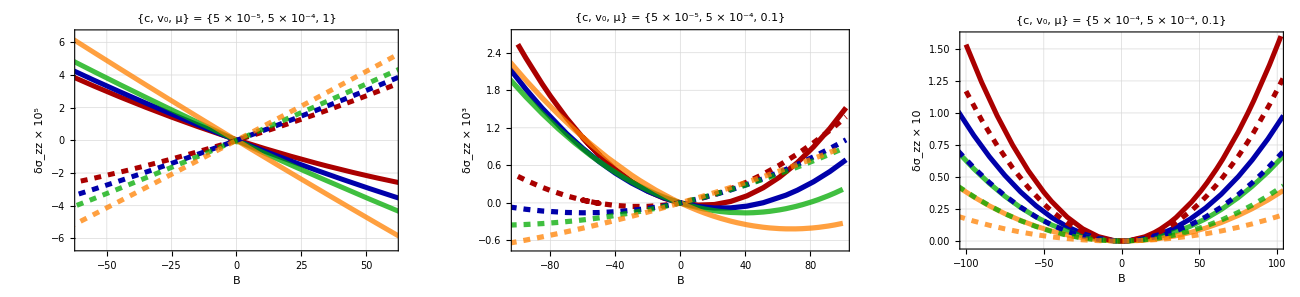

```mathematica
style={(**)Directive[Darker[Red],Thickness[0.008]],(**)Directive[Darker[Blue],Thickness[0.008]],Directive[Darker[Green],Thickness[0.008],Opacity[0.75]],(**)Directive[Orange,Thickness[0.008],Opacity[0.75]](*********),Directive[Darker[Red],Thickness[0.008],Dashed],(**)Directive[Darker[Blue],Thickness[0.008],Dashed],Directive[Darker[Green],Thickness[0.008],Opacity[0.75],Dashed],(**)Directive[Orange,Thickness[0.008],Opacity[0.75],Dashed]};

g1=ListPlot[{d1at11,d1at21,d1at31,d1at41,d1at12,d1at22,d1at32,d1at42},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16],PlotRange->{{-60,60},{-6.5,6.5}},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,Axes->False,FrameLabel->{"B","δσ_zz × 10^5"},FrameTicksStyle->Directive[Bold,Black,12],PlotLabel->Style["{c, v_0, μ} = {5 × 10^-5,  5 × 10^-4, 1}",Bold,Darker[Brown],18],ImageSize->450,GridLines->Automatic];

g2=ListLinePlot[{d2at11,d2at21,d2at31,d2at41,d2at12,d2at22,d2at32,d2at42},(*********)FrameTicksStyle->Directive[Darker[Gray],16],PlotRange->{{-100,100},{-0.7,2.7}},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,Axes->False,FrameLabel->{"B","δσ_zz × 10^3"},FrameTicksStyle->Directive[Bold,Black,12],PlotLabel->Style["{c, v_0, μ} = {5 × 10^-5,  5 × 10^-4, 0.1}",Bold,Darker[Brown],18],ImageSize->470,GridLines->Automatic];

g3=ListLinePlot[{d3at11,d3at21,d3at31,d3at41,d3at12,d3at22,d3at32,d3at42},(*********)FrameTicksStyle->Directive[Darker[Gray],16],PlotRange->{{-100,100},{-0.03,1.6}},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,Axes->False,FrameLabel->{"B","δσ_zz × 10"},FrameTicksStyle->Directive[Bold,Black,12],PlotLabel->Style["{c, v_0, μ} = {5 × 10^-4,  5 × 10^-4, 0.1}",Bold,Darker[Brown],18],ImageSize->450,GridLines->Automatic];


leg=LineLegend[style,{"1, 0.5","1, 1","1, 2","1, 50","-1, 0.5","-1, 1","-1, 2","-1, 50"},LabelStyle->{18,Darker[Brown],Bold},LegendLayout->{"Row",1}];

pl=Legended[GraphicsGrid[{{g1,g2,g3}},Spacings->{20,0},ImageSize->1300],Placed[leg,Below]]
SetDirectory[NotebookDirectory[]];
Export["allwithomm.pdf",Rasterize[pl],ImageResolution->1000];
```